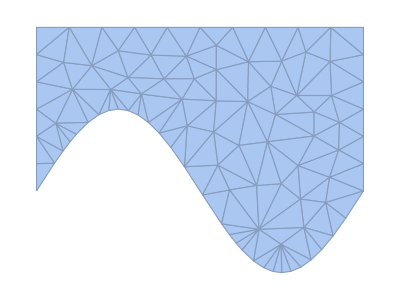

```mathematica
model =DiscretizeRegion[ImplicitRegion[y>= Sin[1/2 π*x] && y <= 2 && 0<=x<=4, {{x,0,4},{y,-1,2}}], MaxCellMeasure->0.1]
```

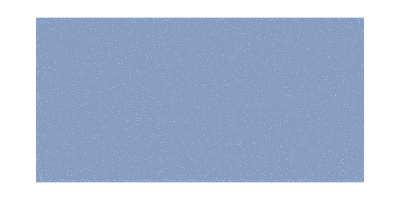

```mathematica
DiscretizeRegion[ImplicitRegion[y>=0 && y <= 2 && 0<=x<=4, {{x,0,4},{y,0,2}}], MaxCellMeasure->0.001]
```

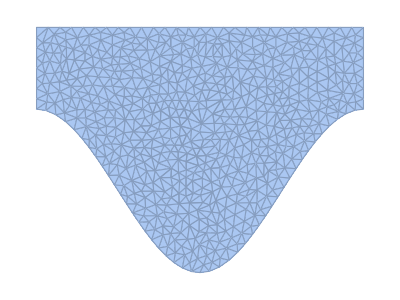

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Sin[1/2 π*x] && y <= 2 && 1<=x<=5, {{x,0,5},{y,-1,2}}], MaxCellMeasure->0.01]
```

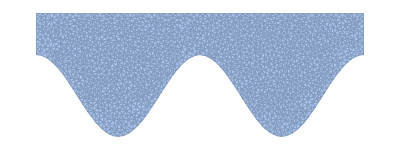

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Sin[1/2 π*x] && y <= 2 && 1<=x<=9, {{x,0,10},{y,-1,2}}], MaxCellMeasure->0.01]
```

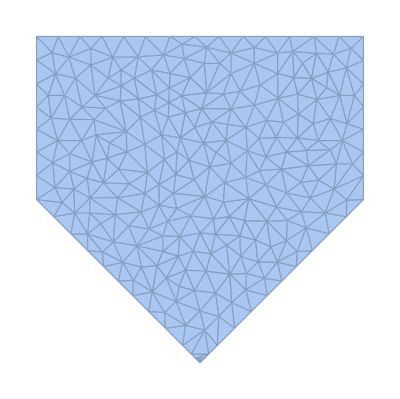

```mathematica
DiscretizeRegion[ImplicitRegion[y>= Abs[x - 1] && y <= 2 && 0<=x<=2, {{x,0,2},{y,-1,2}}], MaxCellMeasure->0.01]
```